```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/WithGaiaErrors/MSTO

Frequencies as a function of the actions

```mathematica
Mtrue=12.2;
btrue=8.0;
OmegaR[Jr_,L_]:=Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2)
OmegaTheta[Jr_,L_]:=(1+L/Sqrt[L^2+4 Mtrue btrue])/2 (Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2))
```

Conversion factor between km/s and kpc/Myr

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Construct streams as clumps in (Jr, L, L_z) space

```mathematica
Ns=3;
sigmas={0.005,.001,.008};(*,0.02,0.05,0.07}*)(*RandomReal[{0,.1},Ns]*)
inclinations=RandomVariate[UniformDistribution[{-π,π}],Ns]
```

{-0.449861,2.85156,3.11746}

```mathematica
inclinations={-0.9437901488480112,2.36759592574413,-2.631874363058749};
```

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/2,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MixtureDistribution[{0.393021,0.442316,0.660672},{MultinormalDistribution[{0.530355,2.75458,0.424308},{{0.0025,0.,0.},{0.,0.005,0.},{0.,0.,0.005}}],MultinormalDistribution[{-0.196636,9.46275,2.23984},{{0.0005,0.,0.},{0.,0.001,0.},{0.,0.,0.001}}],MultinormalDistribution[{-0.532197,3.38998,2.48252},{{0.004,0.,0.},{0.,0.008,0.},{0.,0.,0.008}}]}]

```mathematica
spikyDist=MixtureDistribution[{0.3336438850880812,0.4497490174687988,0.4668006188130658},{MultinormalDistribution[{0.4904000185561226,3.5182031581114668,5.474639235801524},{{0.0025,0.,0.},{0.,0.005,0.},{0.,0.,0.005}}],MultinormalDistribution[{-0.22167261816752726,3.3727794684873373,1.1505882588213936},{{0.0005,0.,0.},{0.,0.001,0.},{0.,0.,0.001}}],MultinormalDistribution[{0.46417940437568683,3.111625369385454,0.03691885857896082},{{0.004,0.,0.},{0.,0.008,0.},{0.,0.,0.008}}]}];
```

```mathematica
Nstars=150000;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{150000,3}

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{150000,3}

### Clustering analysis picks out which points go to which stream so we can choose different inclinations for each COM orbit (θ_1 is a const of the motion)

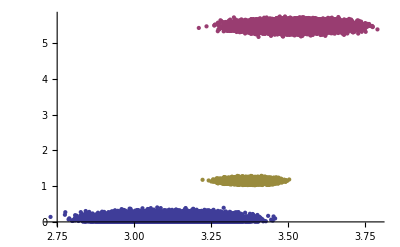

```mathematica
ListPlot[FindClusters[trueActions[[All,{2,3}]],3,Method->"Optimize"]]
```

```mathematica
Dimensions[streamIndex=ClusteringComponents[trueActions,3,1]]
```

{150000}

```mathematica
s1sel=Thread[streamIndex==3];
s2sel=Thread[streamIndex==2];
s3sel=Thread[streamIndex==1];
```

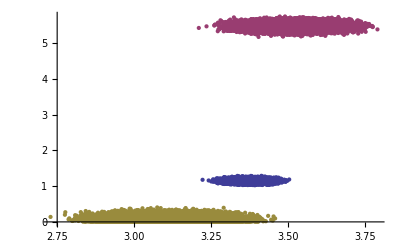

```mathematica
ListPlot[{Pick[trueJrL[[All,{2,3}]],s1sel],Pick[trueJrL[[All,{2,3}]],s2sel],Pick[trueJrL[[All,{2,3}]],s3sel]}]
```

```mathematica
Mean[Pick[trueJrL,s1sel]]
```

{-0.221674,3.37273,1.15054}

```mathematica
Mean[Pick[trueJrL,s2sel]]
```

{0.490766,3.51794,5.47507}

```mathematica
Mean[Pick[trueJrL,s3sel]]
```

{0.464446,3.11112,0.0865517}

```mathematica
incs=Table[0,{i,1,Nstars}];
incs[[Flatten[Position[s1sel,True]]]]=RandomVariate[NormalDistribution[inclinations[[1]],2π/500],Length[Position[s1sel,True]]];
incs[[Flatten[Position[s2sel,True]]]]=RandomVariate[NormalDistribution[inclinations[[2]],2π/500],Length[Position[s2sel,True]]];
incs[[Flatten[Position[s3sel,True]]]]=RandomVariate[NormalDistribution[inclinations[[3]],2π/500],Length[Position[s3sel,True]]];
```

```mathematica
Dimensions[incs]
```

{150000}

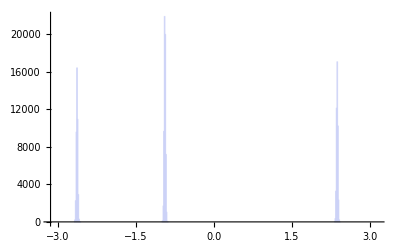

```mathematica
Histogram[incs,{-π,π,2π/500}]
```

### Assign angles

```mathematica
Dimensions[initAngles=Transpose[{incs,Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π],Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π]}]]
```

{150000,3}

### Convert “initial” coordinates to configuration space (x,v) and measure satellite parameters

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,5055,8]

```mathematica
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
ListPointPlot3D[initPositions,PlotRange->{{-50,50},{-50,50},{-50,50}}]
```

-Graphics3D-

```mathematica
Dimensions[streamLists=FindClusters[initPositions,3]]
```

{3}

```mathematica
ListPointPlot3D[{Pick[initPositions,s1sel],Pick[initPositions,s2sel],Pick[initPositions,s3sel]}]
```

-Graphics3D-

```mathematica
Dimensions[iP1=Pick[initPositions,s1sel]]
Dimensions[iP2=Pick[initPositions,s2sel]]
Dimensions[iP3=Pick[initPositions,s3sel]]
```

{61695,3}

{45651,3}

{42654,3}

```mathematica
ListPointPlot3D[{Pick[initVelocities,s1sel],Pick[initVelocities,s2sel],Pick[initVelocities,s3sel]}]
```

-Graphics3D-

```mathematica
meanX1=Mean[iP1]
meanX2=Mean[iP2]
meanX3=Mean[iP3]
```

{9.39537,4.97784,6.5142}

{-7.9004,-23.6873,19.3236}

{4.33128,-6.35833,1.28782}

```mathematica
meanV1=Mean[Pick[initVelocities,s1sel]]
meanV2=Mean[Pick[initVelocities,s2sel]]
meanV3=Mean[Pick[initVelocities,s3sel]]
```

{142.627,-2.2233,375.942}

{7.55323,-190.995,246.09}

{182.817,58.6154,357.654}

```mathematica
Dimensions[dX1=Map[(#-meanX1)&,iP1]]
Dimensions[dX2=Map[(#-meanX2)&,iP2]]
Dimensions[dX3=Map[(#-meanX3)&,iP3]]
```

{61695,3}

{45651,3}

{42654,3}

```mathematica
Dimensions[dV1=Map[(#-meanV1)&,Pick[initVelocities,s1sel]]]
Dimensions[dV2=Map[(#-meanV2)&,Pick[initVelocities,s2sel]]]
Dimensions[dV3=Map[(#-meanV3)&,Pick[initVelocities,s3sel]]]
```

{61695,3}

{45651,3}

{42654,3}

```mathematica
sigX1=StandardDeviation[dX1]
sigX2=StandardDeviation[dX2]
sigX3=StandardDeviation[dX3]
```

{0.159272,0.191657,0.176636}

{0.914359,0.852413,0.728753}

{0.337928,0.15102,0.532805}

```mathematica
Norm[sigX1]
Norm[sigX2]
Norm[sigX3]
```

0.305451

1.44698

0.648756

```mathematica
sigV1=StandardDeviation[dV1]
sigV2=StandardDeviation[dV2]
sigV3=StandardDeviation[dV3]
```

{6.38706,7.9047,3.77342}

{10.985,10.2288,8.74194}

{23.5492,18.9228,14.1182}

```mathematica
Norm[sigV1]
Norm[sigV2]
Norm[sigV3]
```

10.8406

17.3701

33.346

### Evolve angles forward in time using the frequencies

```mathematica
iA1=Pick[initAngles,s1sel];
iA2=Pick[initAngles,s2sel];
iA3=Pick[initAngles,s3sel];

trueJrL1=Pick[trueJrL,s1sel];
trueJrL2=Pick[trueJrL,s2sel];
trueJrL3=Pick[trueJrL,s3sel];
```

```mathematica
iaCOM1=Mean[iA1]
iaCOM2=Mean[iA2]
iaCOM3=Mean[iA3]
```

{-0.943819,1.57075,1.57083}

{2.36761,1.57086,1.57089}

{-2.6318,1.57085,1.57079}

```mathematica
trueJrLCOM1=Mean[trueJrL1]
trueJrLCOM2=Mean[trueJrL2]
trueJrLCOM3=Mean[trueJrL3]
```

{-0.221674,3.37273,1.15054}

{0.490766,3.51794,5.47507}

{0.464446,3.11112,0.0865517}

#### For reference, orbital periods of stream COMs (in Myr)

```mathematica
T1=2π/{OmegaTheta[trueJrLCOM1[[3]],trueJrLCOM1[[2]]],OmegaR[trueJrLCOM1[[3]],trueJrLCOM1[[2]]]}
T2=2π/{OmegaTheta[trueJrLCOM2[[3]],trueJrLCOM2[[2]]],OmegaR[trueJrLCOM2[[3]],trueJrLCOM2[[2]]]}
T3=2π/{OmegaTheta[trueJrLCOM3[[3]],trueJrLCOM3[[2]]],OmegaR[trueJrLCOM3[[3]],trueJrLCOM3[[2]]]}
```

{23.9,13.9608}

{42.8443,25.1773}

{19.8094,11.4453}

#### Evolution time in Myr for each stream

```mathematica
eTimes={410,1250,2000};
```

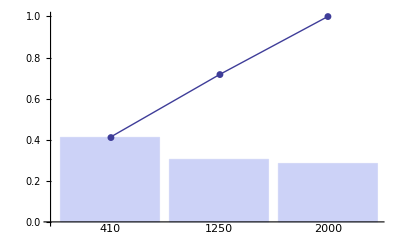

```mathematica
evolTime =Table[0,{i,1,Nstars}];
evolTime[[Flatten[ Position[s1sel,True]]]]=eTimes[[1]];
evolTime[[Flatten[ Position[s2sel,True]]]]=eTimes[[2]];
evolTime[[Flatten[ Position[s3sel,True]]]]=eTimes[[3]];
<<StatisticalPlots`
ParetoPlot[evolTime]
```

#### Evolve centers of mass forward in time to get COM orbit

```mathematica
Dimensions[timeSeries=Table[Table[t,{t,0,eTimes[[i]]}],{i,1,Ns}]]
```

{3}

```mathematica
onesSeries=Table[Table[1,{t,0,eTimes[[i]]}],{i,1,Ns}];
```

```mathematica
Dimensions[tACOM1=Transpose[{iaCOM1[[1]]onesSeries[[1]],Mod[iaCOM1[[2]]+OmegaTheta[trueJrLCOM1[[3]],trueJrLCOM1[[2]]] timeSeries[[1]],2π],Mod[iaCOM1[[3]]+OmegaR[trueJrLCOM1[[3]],trueJrLCOM1[[2]]] timeSeries[[1]],2π]}]]
```

{411,3}

```mathematica
Dimensions[tACOM2=Transpose[{iaCOM2[[1]]onesSeries[[2]],Mod[iaCOM2[[2]]+OmegaTheta[trueJrLCOM2[[3]],trueJrLCOM2[[2]]] timeSeries[[2]],2π],Mod[iaCOM2[[3]]+OmegaR[trueJrLCOM2[[3]],trueJrLCOM2[[2]]] timeSeries[[2]],2π]}]]
```

{1251,3}

```mathematica
Dimensions[tACOM3=Transpose[{iaCOM3[[1]]onesSeries[[3]],Mod[iaCOM3[[2]]+OmegaTheta[trueJrLCOM3[[3]],trueJrLCOM3[[2]]] timeSeries[[3]],2π],Mod[iaCOM3[[3]]+OmegaR[trueJrLCOM3[[3]],trueJrLCOM3[[2]]] timeSeries[[3]],2π]}]]
```

{2001,3}

#### Evolve the full streams forward in time

```mathematica
Dimensions[trueAngles=Transpose[{initAngles[[All,1]],Mod[initAngles[[All,2]]+Thread[OmegaTheta[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π],Mod[initAngles[[All,3]]+Thread[OmegaR[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π]}]]
```

{150000,3}

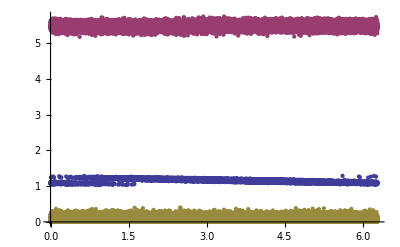

```mathematica
ListPlot[{Transpose[{trueAngles[[Flatten[Position[s1sel,True]],3]],trueJrL[[Flatten[Position[s1sel,True]],3]]}],Transpose[{trueAngles[[Flatten[Position[s2sel,True]],3]],trueJrL[[Flatten[Position[s2sel,True]],3]]}],Transpose[{trueAngles[[Flatten[Position[s3sel,True]],3]],trueJrL[[Flatten[Position[s3sel,True]],3]]}]},PlotRange->{{0,2π},All}]
```

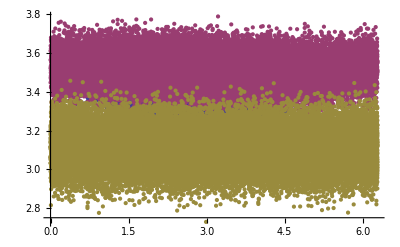

```mathematica
ListPlot[{Transpose[{trueAngles[[Flatten[Position[s1sel,True]],2]],trueJrL[[Flatten[Position[s1sel,True]],2]]}],Transpose[{trueAngles[[Flatten[Position[s2sel,True]],2]],trueJrL[[Flatten[Position[s2sel,True]],2]]}],Transpose[{trueAngles[[Flatten[Position[s3sel,True]],2]],trueJrL[[Flatten[Position[s3sel,True]],2]]}]},PlotRange->{{0,2π},All}]
```

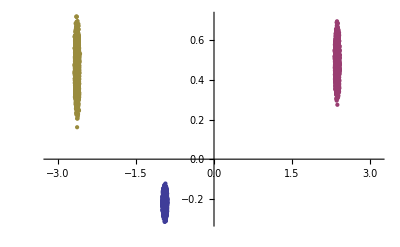

```mathematica
ListPlot[{Transpose[{trueAngles[[Flatten[Position[s1sel,True]],1]],trueJrL[[Flatten[Position[s1sel,True]],1]]}],Transpose[{trueAngles[[Flatten[Position[s2sel,True]],1]],trueJrL[[Flatten[Position[s2sel,True]],1]]}],Transpose[{trueAngles[[Flatten[Position[s3sel,True]],1]],trueJrL[[Flatten[Position[s3sel,True]],1]]}]},PlotRange->{{-π,π},All}]
```

Convert coordinates to configuration space (x,v)

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,5056,8]

```mathematica
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
xvCOM1=Table[{0,0,0,0,0,0},{i,1,Length[tACOM1]}];
xvCOM2=Table[{0,0,0,0,0,0},{i,1,Length[tACOM2]}];
xvCOM3=Table[{0,0,0,0,0,0},{i,1,Length[tACOM3]}];
```

```mathematica
Dimensions[xvCOM1]
```

{411,6}

```mathematica
Length[tACOM1]
```

411

```mathematica
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
```

```mathematica
For[i=1,i≤ Length[tACOM1],i++,xvCOM1[[i]]=AAToCart[trueJrLCOM1,tACOM1[[i]]]]
For[i=1,i≤ Length[tACOM2],i++,xvCOM2[[i]]=AAToCart[trueJrLCOM2,tACOM2[[i]]]]
For[i=1,i≤ Length[tACOM3],i++,xvCOM3[[i]]=AAToCart[trueJrLCOM3,tACOM3[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
tP1=Pick[truePositions,s1sel];
tP2=Pick[truePositions,s2sel];
tP3=Pick[truePositions,s3sel];
```

```mathematica
xCOM1=xvCOM1[[All,1;;3]];
xCOM2=xvCOM2[[All,1;;3]];
xCOM3=xvCOM3[[All,1;;3]];
```

```mathematica
boxsize=30;
```

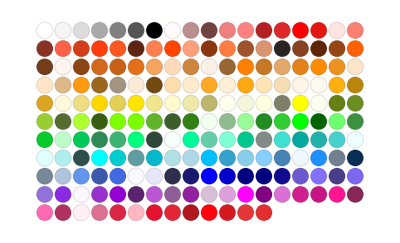

```mathematica
ColorData["Legacy","Panel"]
```

```mathematica
myYellow=ColorData["Legacy"]["CadmiumLemon"]
```

RGBColor[1.,0.889996,0.009995]

```mathematica
threeStreams=Show[ListPointPlot3D[{iP1,iP2,iP3},PlotStyle->{Lighter[Lighter[Red]],Lighter[Lighter[Green]],Lighter[Lighter[Blue]]},PlotRange->{{-boxsize,boxsize},{-boxsize,boxsize},{-boxsize,boxsize}}],Graphics3D[{Lighter[Red],Line[xCOM1],Lighter[Green],Line[xCOM2],Lighter[Blue],Line[xCOM3]}],ListPointPlot3D[{tP1,tP2,tP3},PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]}],Graphics3D[{Cyan,Opacity[0.2],Sphere[{-8.5,0,0},10],(*Opacity[0.1],Sphere[{-8.5,0,0},25],*)Black,Opacity[1],Thickness[0.002],Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]}],Graphics3D[{Glow[myYellow],Black,Sphere[{-8.5,0,0},2]}],AspectRatio->1,AxesStyle->Directive[FontFamily->"Helvetica",FontSize->18],AxesLabel->{"x (kpc)","y (kpc)","z (kpc)"}]
```

-Graphics3D-

```mathematica
Dimensions[Transpose[{truePositions[[All,1]]-8.0, truePositions[[All,2]],truePositions[[All,3]]}]]
```

{15000,3}

```mathematica
Dimensions[dists=Map[Norm,Transpose[{truePositions[[All,1]]-8.0, truePositions[[All,2]],truePositions[[All,3]]}]]]
```

{150000}

```mathematica
{Min[dists],Max[dists]}
```

{4.50494,46.5716}

```mathematica
Show[ListColorPlot[truePositions[[All,1]],truePositions[[All,3]],dists,.1,"Rainbow","x (kpc)","z (kpc)"],MyColorBar[{Min[dists],Max[dists]},5,"D"]]
```

-Graphics-

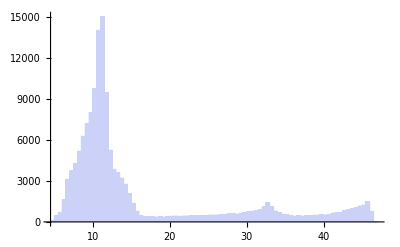

```mathematica
Histogram[dists,PlotRange->All]
```

```mathematica
DumpSave["threeStreamsNearby150k.mx",{truePositions,trueVelocities,trueCart,trueJrL,trueActions,trueAngles,s1sel,s2sel,s3sel,initAngles,Nstars,Ns}];
```